## Power law fit: Verify consistency with free-free emission from outflow (https://www.aanda.org/articles/aa/pdf/2006/03/aa2160-04.pdf)

```mathematica
data = {{3.6,0.33549232*10^(-3)},{4.5, 0.28204535*10^(-3)},{5.8,0.21036669*10^(-3)},{8.0,0.19616618*10^(-3)}}
```

{{3.6,0.000335492},{4.5,0.000282045},{5.8,0.000210367},{8.,0.000196166}}

```mathematica
wl = {3.6,4.5,5.8,8.0}
```

{3.6,4.5,5.8,8.}

```mathematica
errors = {0.02010765,0.01171112,0.03456009,0.03161511}*10^(-3)
```

{0.0000201077,0.0000117111,0.0000345601,0.0000316151}

```mathematica
nlm = NonlinearModelFit[data,b x^c, {b,c},x, Weights -> 1/errors]
```

FittedModel[0.000876392/x^0.755816]

```mathematica
nlm[{"BestFit","ParameterTable"}]
```

{0.000876392/x^0.755816, | Estimate | Standard Error | t-Statistic | P-Value
b | 0.000876392 | 0.000157222 | 5.57423 | 0.0307085
c | -0.755816 | 0.119225 | -6.33939 | 0.0239913}

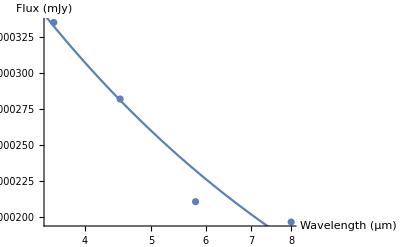

```mathematica
Show[ListLogLinearPlot[data],LogLinearPlot[nlm[{"BestFit"}],{x,3.0,9.0}], AxesLabel->{"Wavelength (μm)", "Flux (mJy)"}]
```

```mathematica
0.76-0.122
```

0.638